```mathematica
ftophat[s_, r_] := (Tanh[s (r+R)]-Tanh[s (r-R)])/(2Tanh[s R])
```

```mathematica
R=1
```

1

```mathematica
σ = 23
```

23

The following shows the tophat nature of the f function that multiplies the velocity in the β displacement element

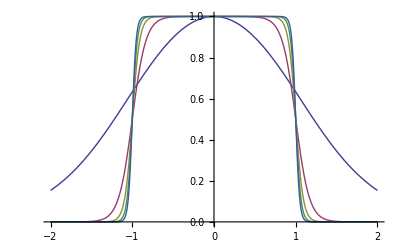

```mathematica
Plot[Evaluate[Table[ftophat[s, r], {s, 1, 23, 5}]], {r, -2, 2}]
```

```mathematica
D[(Tanh[s (r+R)]-Tanh[s (r-R)])/(2Tanh[s R]), r]
```

1/2 Coth[s] (-s Sech[(-1+r) s]^2+s Sech[(1+r) s]^2)

There’s got to be a better way to write down this function than what I’m doing here (longhand)

```mathematica
theta[x_, rho_, s_, xs_] = (x-xs)/(((x-xs)^2+rho^2)^(1/2))(1/2 Coth[s] (-s Sech[(-1+((x-xs)^2+rho^2)^(1/2)) s]^2+s Sech[(1+((x-xs)^2+rho^2)^(1/2)) s]^2))
```

((x-xs) Coth[s] (-s Sech[s (-1+√(rho^2+(x-xs)^2))]^2+s Sech[s (1+√(rho^2+(x-xs)^2))]^2))/(2 √(rho^2+(x-xs)^2))

```mathematica
Plot3D[theta[x, rho, 8, 27], {x,25.5,28.5}, {rho, -1.5, 1.5}, PlotRange->{-4,4}]
```

-Graphics3D-